# The New Seeker

Brian Beckman
17 Aug 2019

## Abstract

We can find a 2,000-dimensional needle in a 2,000-dimensional haystack more than 80% of the time in fewer than 160,000 sequential judgments. We once succeeded in finding a 5,000-dimensional needle in a 5,000-dimensional haystack in 1.3 million judgments; that episode took a couple of days of computer time to run, so we haven’t repeated it yet.

More generally, we show a method of searching for random constant d-vector targets using nothing but binary preference judgments. Judgments simulate human-preference learning. Human-preference learning is interesting because it is cheap at the scale of thousands to millions of judgments. We want to estimate N, the number of judgments needed to find a local maximum of some real-valued benefit function. That estimate comes along with a second hyperparameter, the shrinkage factor Δ, explained below. We cannot find N without specifying Δ and vice versa. N and Δ are linked in a way we do not fully understand. However, we are able to find good pairs: values of N and Δ where searches succeed most or even all of the time. The simulation in this notebook is singly convex, i.e., there is only one local maximum. Real search spaces may be multiply convex: there may be more than one acceptable local maximum. Therefore, the estimated Ns in this notebook are conservative: real-world judgment counts could be many fewer if searches can find an acceptable local maximum.

One of our simulated judgments 
	1. starts with two Gaussian guesses, A and B, centered at the current best estimate y_p of the target and within a statistical search radius σ_p, the standard deviation of the Gaussian pseudo-random number generator
	2. consults an oracle for the Euclidean distance from the true target for each of A and B
	3. re-centers the next search at at the closer of the two: y_p←A if A is closer to true target, else y_p←B, and sets a slightly smaller search radius (σ_p←Δ σ_p;Δ<1), explaining Δ

A trial is a sequence of judgments. 2,000 dimensions with a maximum “gas-tank” of 160,000 judgments is the biggest trial in this notebook. Tt can take a couple of minutes to run on one core. We call the maximum number of judgments, say 160,000, that we’re willing to wait, a gas tank, because we fail a search when it “runs out of gas,” that is, takes more judgments than we are willing to wait. We express how long we’re willing to wait for by putting a number like 160,000 in the gas tank. 

We do episodes of 1600 trials in 16 rollouts of 100 trials each. Each rollout tries a different shrinkage factor Δ. It takes Mathematica about six hours on six cores in 64 GB of memory for an episode at 2,000 dimensions and a gas tank of 160,000. That’s about half a billion 2000-vectors, or about a trillion Gaussian samples. In another place, we ran a C++ version of this code, and found a 5,000 D needle in a 5,000 D haystack in 1.3 million judgments. That was the biggest episode we’ve done so far with any software. We do not yet know whether Mathematica can do an episode that big. There is a secondary, software-engineering story about C++ versus Mathematica that we report in another tech report.

## Searching for Shrinkage

We sweep the the shrinkage factor Δ in an episode, one Δ in each of 16 rollouts, looking for the best Δ for a given d and maxIter, the size of the gas tank. What’s the shrinkage factor? Every time we make a judgment, the search re-centers at the preferred point, and the search radius σ_p shrinks a little bit, by Δ<1. For our biggest episode ever in C++, in 5,000 dimensions and a gas-tank of 10,000,000 judgments, the best Δ found is 0.99999. For our biggest episode in this notebook, with d=2000 and maxIter=160000, the best Δ is 0.999919. We’re more confident in the d=2000 number than in the d=5000 number because the latter was a lucky shot rather than the result of a sweep.

## How a Trial “dies” or “wanders”

Generally speaking, when Δ is too small, the search radius decreases too quickly (the rate of decrease is Δ-1), and the trial will run out of gas before it gets close to the target. We can tell, ahead of time, that we will run out of gas, and we can cut off the trial early, before we actually run out of gas ("We're never going to make it to Bakersfield; might as well turn around now"). The point of quitting early is to save wall-clock time. These episodes take many hours each to run and anything we can do to speed them up is worth the trouble. We predict running out of gas when the distance dist of y_p from the target is greater than 10×maxIter×σ_p; we guess that we're probably not going to get there in 10×maxIter more tries even if σ_p weren't decreasing every step; we don't have enough gas by an order of magnitude. We call such a trial "dead." This prediction is just a heuristic. We might find a better one with harder theoretical thinking. However, we have a way to find out whether this prediction is too aggressive, i.e., kills the trial too early: run some trials with the death-predictor off, in small dimensions so they complete in tolerable time, and compare them to trials in the same number of dimensions with the predictor on. If our predictor is not too aggressive, then the convergence rates with the predictor on or off should be about the same. If the predictor is too strong, then the convergence rate will be higher with the predictor off.

When Δ is too big, we never find the target because our search radius is always too big; it doesn't decrease quickly enough. Such trials are called “wandering.”

### Algorithm

Given dimension d≥2, shrinkage factor Δ<1, tolerance tol=0.01, current iteration number i, and "gas tank" maxIter≥1, choose a target d-vector uniformly in the d-ball.

Set y_p←{0}_(ℝ^d), σ_p←1 (covariance matrix=𝟙_(ℝ^d)).

If i≥maxIter, throw “Wandering.”

Calculate dist=||y_p-target(||)_(L_2^d), Euclidean distance of current best estimate y_p to target.

If dist>10×maxIter×σ_p, throw “Dead.”

Generate guesses A and B, each normally distributed (Gaussian) with center y_p and standard deviation σ_p.

Calculate the Euclidean distances d_A=||y_p-A(||)_(L_2^d) and d_B=||y_p-B(||)_(L_2^d) .

If d_A<tol or d_B<tol, throw “Found.”

If d_A<d_B, set y_p←A, else set y_p←B .

Set σ_p←Δ σ_p, i←i+1

Go to 3.

In Mathematica, we iterate steps 11→3 with a fast, elegant, functional fold. Fold may be more familiar by the Python name reduce or by the C# name Aggregate. In C++, we iterate rollouts in an episode in parallel threads.

### DEFINITIONS

```mathematica
({{Style["Term",Bold,Italic], Style["synonym",Bold,Italic], Style["description",Bold,Italic]}, {"Episode", "rollouts", "parallelizable bunch of rollouts"}, {"Rollout", "trials", "parallelizable bunch of trials"}, {"Trial", "trajectory, trip", "non-parallelizable sequence of judgments"}, {"Judgment", "", "choice of one of two guesses, A and B"}, {"Guess", "", "a d-vector"}})//TableForm
```

Term | synonym | description
Episode | rollouts | parallelizable bunch of rollouts
Rollout | trials | parallelizable bunch of trials
Trial | trajectory, trip | non-parallelizable sequence of judgments
Judgment |  | choice of one of two guesses, A and B
Guess |  | a d-vector

## Sampling

## Uniform in d-Ball—2 [ n, d ]

This algorithm exploits Archimedes’s “hat-box” algorithm and is the fastest known (see Ops Robotics Tech Report 018). By default, it generates 50,000 uniformly random vectors in 2 dimensions, but it works in any number of dimensions greater than or equal to 2.

```mathematica
ClearAll[uniformInBall2];
uniformInBall2[n_:50000,d_:2]:=
Drop[#,2]&/@
Normalize/@
RandomVariate[
NormalDistribution[],{n,d+2}];
```

There follows a visual demonstration of uniformity.

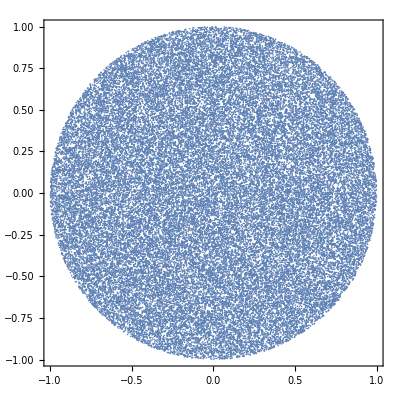

```mathematica
ListPlot[uniformInBall2[],AspectRatio->Automatic,Frame->True]
```

There follows a function for generating a single, uniform, random d-vector for a target.

```mathematica
ClearAll[getTarget];
getTarget[d_:4]:=uniformInBall2[1,d]⟦1⟧;
```

## Seeking

## Bisecting for the Decay

For each dim, tol, maxIter; find, via bisection, the smallest decay Δ that converges the most rollouts in an episode, i.e., in the smallest number of a/b judgments on the average. Bisection is “divide-and-conquer” search, i.e., runs in logarithmic time. However, we must bisect on both Δ and maxIter simultaneously. Our software does not automatically do that, so we bisect manually for now (TODO).

### Do One Judgment

The following function, doJudgment, performs one judgment. It throws when it dies, wins, or wanders, so the caller handles all cases in Catch blocks. It decays standard deviation σ rather than covariance, σ^2. Some versions of seeker decay the covariance instead. I don't think it matters.

Call doJudgment from Fold wrapped in three nested Catches, one each for “Found,” “Dead,” and “Wandering.” Optionally, doJudgment sows out intermediate points, where the caller can reap them for visualization, logging, debugging. Sow uses memory, so we must stub it out for the biggest runs. doJudgment calls Sow through a pointer, sow, in lower case. Set sow to Identity when you don’t need the intermediate points. Likewise, deathTest defaults to True; set it temporarily (in a Block) to False for the purpose of determining whether the death test affects results. If the death test is too aggressive, you will get more convergence with deathTest set to False.

```mathematica
(* set "sow" to "Identity" to save time when you don't need to reap. *)
sow=Sow;
deathTest=True;
ClearAll[doJudgment,nexter002];
doJudgment[{yp_,dist_,σ_},{Δ_,tar_,tol_,maxIter_,i_}]:=
(* 8 parameters; account for all of them: *)
Module[{a,b,da,db,d},

(* (2) dist, σ used *)
If[(deathTest && (dist>10maxIter σ)),Throw[{yp,dist,σ,tar,Δ,i},"Dead"]];

(* (4) maxIter, i used *)
If[i≥maxIter,Throw[{yp,dist,σ,tar,Δ,i},"Wandering"]]; 

(* (5) yp used *)
a=Map[RandomVariate[NormalDistribution[#,σ]]&,yp];
(* (6) tar used *)
da=EuclideanDistance[tar,a];
(* (7) tol used *)
If[da<tol,Throw[{a,da,σ,tar,Δ,i},"Found"]];

b=Map[RandomVariate[NormalDistribution[#,σ]]&,yp];
db=EuclideanDistance[tar,b];
If[db<tol,Throw[{b,db,σ,tar,Δ,i},"Found"]];

(* (8) Δ used *)
With[{νσ=Quiet[σ*Δ]},
sow@If[da<db,
{a,da,νσ},
{b,db,νσ}]]];
```

### Convenient Form for Output

The following converts outputs from position-sensitive list form to convenient Association form (like dictionary in Python).

```mathematica
ClearAll[trialDict];
trialDict[{yp_,dist_,σ_,tar_,Δ_,i_},tag_]:=
<|"yp"->yp,"dist"->dist,"σ"->σ,"tar"->tar,"Δ"->Δ,"i"->i,"tag"->tag|>;
```

### Number of Nines in Δ

It’s best to represent Δ logarithmically. We want an integer that specifies the number of nines in a Δ. The following function, ΔFromLd, and its inverse, ldFromΔ, do that job.

```mathematica
ClearAll[ldFromΔ,ΔFromLd];
ldFromΔ[Δ_]:=-Log10[1.-Δ];
ΔFromLd[lm_]:=1.-10.^-lm;
```

```mathematica
Table[{ld,NumberForm[ΔFromLd[ld],9]},
{ld,1,7,0.5}]//Grid
```

1. | 0.9
1.5 | 0.968377223
2. | 0.99
2.5 | 0.996837722
3. | 0.999
3.5 | 0.999683772
4. | 0.9999
4.5 | 0.999968377
5. | 0.99999
5.5 | 0.999996838
6. | 0.999999
6.5 | 0.999999684
7. | 0.9999999

The following is a visualization form that allows you to experiment, interactively, with all the hyperparameters. The central computation is highlighted: it calls Fold over doJudgment under three, nested Catches and a Reap.

```mathematica
ClearAll[vizSeek2D,vizSeek2D002,dist,yp,σ,cov,i];
picker[n_]:=#⟦n⟧&;{yp,dist,σ}=picker/@Range[3];
echo=Echo;
DBALLRADIUS=1.0;
vizSeek2D002[tol_:0.1,Δ_:0.99599,maxIter_:10000,pr_:10,dim_:2]:=
(* For picking a random pair of dims for display from big-dim vectors. *)
With[{indices=Sort@RandomSample[Range[dim],2]},
With[{indexer={#⟦indices⟦1⟧⟧,#⟦indices⟦2⟧⟧}&},
With[{sampler={indexer[yp[#]],dist[#],σ[#]}&},
With[{tar=getTarget[dim],ini=ConstantArray[0,dim]},
With[{result=Reap[Catch[Catch[Catch[Fold[
doJudgment,{ini,0,DBALLRADIUS},
Table[{Δ,tar,tol,maxIter,i},{i,maxIter}]],
"Found",trialDict],"Dead",trialDict],"Wandering",trialDict]
]},
With[{tag=result⟦1⟧["tag"],points=result⟦2,1⟧,smtar=indexer@tar,sampled=sampler/@result⟦2,1⟧,l=Length[result⟦2,1⟧]},
Show[Graphics[{
LightGray,Disk[],White,Disk[smtar,0.3],Black,Circle[smtar,0.3],
MapIndexed[
{Hue[(2.+#2*4/l)/6.],Circle[yp[#1],σ[#1]],Point[yp[#1]]}&,
sampled],
Text[Style[{l,tag(*,Δ,tol*),σ[Last[sampled]]},"Text",Background->White],{0,pr*0.960}]
}],AspectRatio->Automatic,Frame->True,PlotRange->1.025*pr]]]]]]];
Manipulate[
vizSeek2D002[10.^le,1.-10^-ld,Floor[10.^lm],r,dim],
Row[{Button["  DO AGAIN  ",(le++;le--)&],"    ",
Button["  RESET  ",(le=-2;ld=1.0;lm=2;r=2;dim=2)&]}],
{{le,-2,"log_10(tol)"},-5,0,0.1,Appearance->{"Open","Labeled"}},
{{ld,1.0,"-log_10(1-Δ)"},0.,5.,0.25,Appearance->{"Open","Labeled"}},
{{lm,3,"log_10(reps)"},0,7,1,Appearance->{"Open","Labeled"}},
{{r,2,"plot range"},1,30,1,Appearance->{"Open","Labeled"}},
{{dim,2},{2,5,10,20,50,100,200,500,1000,2000,5000,10000},ControlType->Setter}]
```

The following are fast, running statistics in constant memory. See http://vixra.org/abs/1606.0328.

```mathematica
ClearAll[cume,zeroStats];
zeroStats=<|"mean"->0,"min"->Infinity,"max"->-Infinity,"var"->0,"n"->0,"stddev"->0|>;
cume[runningStats_,z_]:=
With[{
m=runningStats["mean"],
max=runningStats["max"],
min=runningStats["min"],
n=runningStats["n"],
var=runningStats["var"]},
With[{K=1./(n+1.),r=z-m},
With[{var2=((n-1)var+K n r^2)/Max[1,n]},
<|"mean"->m+K r,"n"->n+1,"min"->Min[z,min],
"max"->Max[z,max],"var"->var2,"stddev"->Sqrt[var2]|>]]];
(*FoldList[cume,zeroStats,{55,89,144}]*)
```

Here is a version that does not Sow all its points, to save memory and time (but mostly memory)

```mathematica
Block[{sow=Identity},
ClearAll[trial];
trial[Δ_,tar_,tol_,maxIter_]:=
Module[{tagg},
Catch[Catch[Catch[
Fold[doJudgment,
{ConstantArray[0.,Length@tar],0.,1.},
Table[{Δ,tar,tol,maxIter,i},{i,maxIter}]],
"Found",trialDict],"Dead",trialDict],"Wandering",trialDict]];
trial[.99599,getTarget[2],0.01,1000]]
```

<|yp→{0.277185,0.128284},dist→0.00372375,σ→0.0782809,tar→{0.277017,0.132004},Δ→0.99599,i→635,tag→Found|>

Here is a form that tests the block that does not Sow. It Reaps nothing, but we did not change the call to Reap so as to avoid the risk of breaking fragile copy-paste code (and we should not copy-paste!)

```mathematica
ClearAll[printSeek2D002];
printSeek2D002[tol_:0.1,Δ_:0.99599,maxIter_:10000,pr_:10,dim_:2]:=
Block[{sow=Identity},
(* For picking a random pair of dims for display from big-dim vectors. *)
With[{indices=Sort@RandomSample[Range[dim],2]},
With[{indexer={#⟦indices⟦1⟧⟧,#⟦indices⟦2⟧⟧}&},
With[{sampler={indexer[yp[#]],dist[#],σ[#]}&},
With[{tar=getTarget[dim],ini=ConstantArray[0,dim]},
With[{result=Reap[Catch[Catch[Catch[Fold[
doJudgment,{ini,0,DBALLRADIUS},
Table[{Δ,tar,tol,maxIter,i},{i,maxIter}]],
"Found",trialDict],"Dead",trialDict],"Wandering",trialDict]]},
<|"σ"->result⟦1⟧["σ"],"i"->result⟦1⟧["i"],"tag"->result⟦1⟧["tag"],"Δ"->Δ,"dim"->dim,"tol"->tol|>]]]]]];
Manipulate[
printSeek2D002[10.^le,1.-10^-ld,Floor[10.^lm],r,dim],
Row[{Button["  DO AGAIN  ",(le++;le--)&],"    ",
Button["  RESET  ",(le=-2;ld=1.0;lm=2;r=2;dim=2)&]}],
{{le,-2,"log_10(tol)"},-5,0,0.1,Appearance->{"Open","Labeled"}},
{{ld,1.0,"-log_10(1-Δ)"},0.,5.,0.25,Appearance->{"Open","Labeled"}},
{{lm,3,"log_10(reps)"},0,7,1,Appearance->{"Open","Labeled"}},
{{r,2,"plot range"},1,30,1,Appearance->{"Open","Labeled"}},
{{dim,2},{2,5,10,20,50,100,200,500,1000,2000,5000,10000},ControlType->Setter}]
```

A bunch of rollouts is an Episode. We might have called this next routine “doEpisode.”

```mathematica
ClearAll[doRollouts];
doRollouts[Δ_,maxRol_,tar_,tol_,maxIter_]:=
Module[{irol,stats=<|"Found"->zeroStats,"Dead"->zeroStats,"Wandering"->zeroStats|>},
For[irol=1,irol≤maxRol,irol++,
With[{result=trial[Δ,tar,tol,maxIter]},
stats@result@"tag"=cume[stats@result@"tag",result@"i"]]];
Append[stats,<|"maxRol"->maxRol,"dim"->Length@tar,"tol"->tol,"Δ"->Δ,"ld"->ldFromΔ@Δ,"maxIter"->maxIter|>]];
doRollouts[0.925,100,getTarget[2],0.01,1000]
```

<|Found→<|mean→52.6786,n→84,min→21,max→88,var→160.365,stddev→12.6635|>,Dead→<|mean→148.312,n→16,min→117,max→178,var→414.496,stddev→20.3592|>,Wandering→<|mean→0,min→∞,max→-∞,var→0,n→0,stddev→0|>,maxRol→100,dim→2,tol→0.01,Δ→0.925,ld→1.12494,maxIter→1000|>

“Bisect” does not work.

```mathematica
ClearAll[bisect,bisectΔ,pctFound,pctDead,pctWandering,pctFailed,costOfFinding,nJudgments];

nJudgments[episode_]:=episode["Found"]["n"]+episode["Dead"]["n"]+episode["Wandering"]["n"];
pctFound[episode_]:=((100.0 episode["Found"]["n"])/nJudgments[episode]);
pctDead[episode_]:=((100.0episode["Dead"]["n"])/nJudgments[episode]);
pctWandering[episode_]:=((100.0episode["Wandering"]["n"])/nJudgments[episode]);
pctFailed[episode_]:=(100.0(episode["Dead"]["n"]+episode["Wandering"]["n"])/nJudgments[episode]);
costOfFinding[episode_]:=episode["Found"]["mean"];
ClearAll[logarithmicMeanΔ];
logarithmicMeanΔ[l_,r_]:=ΔFromLd[Mean[{ldFromΔ@l,ldFromΔ@r}]];

ClearAll[bisect];
bisect[leftΔ_,rightΔ_,maxRol_,tar_,tol_,maxIter_]:=
With[{midΔ=logarithmicMeanΔ[leftΔ,rightΔ]},
With[{
l=echo@doRollouts[leftΔ,maxRol,tar,tol,maxIter],
r=echo@doRollouts[rightΔ,maxRol,tar,tol,maxIter],
m=echo@doRollouts[midΔ,maxRol,tar,tol,maxIter]},
<|"successes"->pctFound/@{l,m,r},
"deaths"->pctDead/@{l,m,r},
"failed"->pctFailed/@{l,m,r},
"wandering"->pctWandering/@{l,m,r},
"costs"->costOfFinding/@{l,m,r}|>
]];

(*Block[{echo=Echo},
bisect[0.9,0.9999999,100,getTarget[20],0.01,1000]]*)

ClearAll[sweep];
sweep[lld_,rld_,nδld_,maxRol_,tar_,tol_,maxIter_]:=
ParallelMap[
echo@doRollouts[ΔFromLd@#,maxRol,tar,tol,maxIter]&,
Range[lld,rld,(rld-lld)/nδld],
Method->"FinestGrained"];

(*adHoc$=Block[{echo=Echo},
sweep[1.875,2.1875,16,100,getTarget@20,0.01,1000]];*)
```

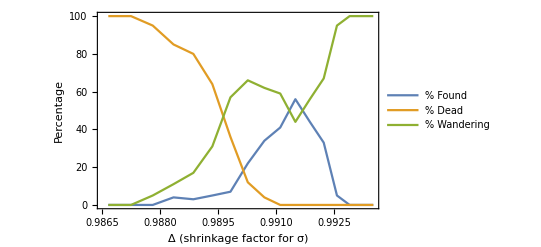

```mathematica
ClearAll[experiment];
experiment[lld_,rld_,nδld_,maxRol_,dim_,tol_,maxIter_,theEchoer_]:=
With[{data=Block[{echo=theEchoer},
sweep[lld,rld,nδld,maxRol,getTarget@dim,tol,maxIter]]},
With[{Δs=#["Δ"]&/@data},
ListLinePlot[{{Δs,pctFound/@data}ᵀ,{Δs,pctDead/@data}ᵀ,{Δs,pctWandering/@data}ᵀ},
Frame->True,
FrameLabel->{{"Percentage",""},
{"Δ (shrinkage factor for σ)",
"Seeker versus Δ, dim = "<>ToString[dim]<>", # rollouts = "<>ToString[maxRol]<>"\ntolerance = "<>ToString[tol]<>", # iters/rollout = "<>ToString[maxIter]}},
PlotLegends->{"% Found","% Dead","% Wandering"}]]];
experiment[1.875,2.1875,16,100,20,0.01,1000,Identity]
```

```mathematica
(*experiment[ldFromΔ@0.99985,ldFromΔ@0.99995,16,100,2000,0.01,80000,Identity]*)
```

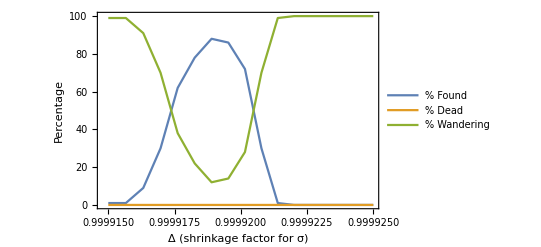

```mathematica
experiment[ldFromΔ@0.999915,ldFromΔ@0.999925,16,100,2000,0.01,160000,Identity]
```

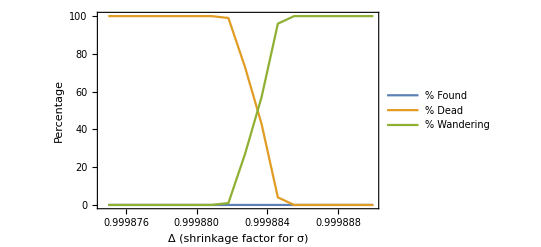

```mathematica
(*experiment[ldFromΔ@0.999875,ldFromΔ@0.99989,16,100,2000,0.01,80000,Identity]*)
```

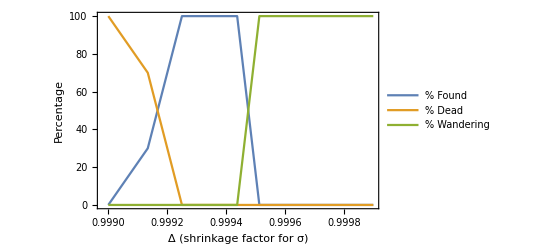

```mathematica
(*experiment[ldFromΔ@0.999,ldFromΔ@0.9999,16,100,200,0.01,20000,Identity]*)
```

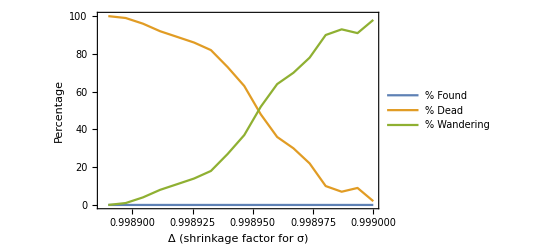

```mathematica
(*experiment[ldFromΔ@0.99889,ldFromΔ@0.999,16,100,200,0.01,10000,Identity]*)
```

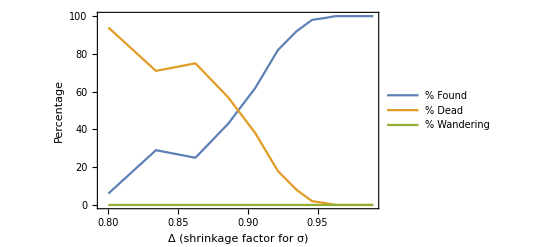

```mathematica
experiment[ldFromΔ@0.80,ldFromΔ@0.99,16,100,2,0.01,1000,Identity]
```

## Junkyard

```mathematica
With[{d=16,l=30/16,r=35/16},ParallelMap[Identity,Range[l,r,(r-l)/d]]]
```

{15/8,485/256,245/128,495/256,125/64,505/256,255/128,515/256,65/32,525/256,265/128,535/256,135/64,545/256,275/128,555/256,35/16}

```mathematica
With[{d=16,l=30/16,r=35/16},Table[l+i(r-l)/d,{i,0,d}]]
```

{15/8,485/256,245/128,495/256,125/64,505/256,255/128,515/256,65/32,525/256,265/128,535/256,135/64,545/256,275/128,555/256,35/16}

```mathematica
Manipulate[
NumberForm[{ΔFromLd@l,ΔFromLd@r,
logarithmicMeanΔ[ΔFromLd@l,ΔFromLd@r]},20],
{{l,1},0,7,1,ControlType->Setter},{{r,7},0,7,1},ControlType->Setter]
```

Test tail-recursion.

```mathematica
ClearAll[testf$];
With[{groundTruth=0.75},
testf$[left_,right_]:=
With[{x=RandomReal[{left,right}]},
If[x<groundTruth,testf$[x,right],
If[x>groundTruth,testf$[left,x],
x]]]];
```

```mathematica
Length@Trace@testf$[0.,1.]
```

433